# Clancey et al. Mechanistic Model (STOPPP)

## SIR Model with Waning Antibodies and Waning Immunity

N is the total population size, S is the number of susceptible individuals, Ι  is the number of infected individuals, R_A is the number of seropositive  and recovered individuals, and R_T is the number of seronegative and recovered individuals.

```mathematica
Ν̇=Ṡ+Ι̇+OverDot[RA] + OverDot[RT]
```

OverDot[RA]+OverDot[RT]+Ṡ+Ι̇

```mathematica
Ṡ=b Ν-β S Ι- S (μ+k Ν )+ Subscript[ω, T] RT
```

-S β Ι+b Ν-S (μ+k Ν)+RT ω_T

```mathematica
Ι̇=β S Ι-γ Ι - Ι(μ+k Ν )
```

S β Ι-γ Ι-Ι (μ+k Ν)

```mathematica
OverDot[RA] =γ Ι- RA(μ+k Ν )- Subscript[ω, A] RA
```

γ Ι-RA (μ+k Ν)-RA ω_A

```mathematica
OverDot[RT]=Subscript[ω, A] RA- RT(μ+k Ν )- Subscript[ω, T] RT
```

-RT (μ+k Ν)+RA ω_A-RT ω_T

## Equilibria and ℛ_0

### Disease Free Equilibria (DFE)

```mathematica
Ν̇=FullSimplify[Ṡ+Ι̇+OverDot[RA]+OverDot[RT]]/.{RA+RT+S+Ι->Ν}
```

b Ν-Ν (μ+k Ν)

```mathematica
Solve[Ν̇==0, Ν]
```

{{Ν→0},{Ν→(b-μ)/k}}

```mathematica
Solve[(Ṡ/. {Ε->0,Ι->0,RA->0, RT->0})==0,S]/.{Ν->(b-μ)/k}
```

{{S→(b-μ)/k}}

```mathematica
DFE= {S->(b-μ)/k,Ε->0,Ι->0,RA->0, RT->0};
```

### Pathogen Present Equilibria

```mathematica
FullSimplify[Solve[{0==Ṡ, 0==Ι̇, 0==OverDot[RA] , 0==OverDot[RT]},{S,Ι, RA, RT}]/.{Ν->(b-μ)/k}]
```

{{S→(b-μ)/k,Ι→0,RA→0,RT→0},{S→(b+γ)/β,Ι→-((b (k-β)+k γ+β μ) (b+ω_A) (b+ω_T))/(k β ((b+γ) (b+ω_T)+ω_A (b+γ+ω_T))),RA→-(γ (b (k-β)+k γ+β μ) (b+ω_T))/(k β ((b+γ) (b+ω_T)+ω_A (b+γ+ω_T))),RT→-(γ (b (k-β)+k γ+β μ) ω_A)/(k β ((b+γ) (b+ω_T)+ω_A (b+γ+ω_T)))}}

## Calculate ℛ_0 using the Next Generation Method (NGM)

### Build vectors ℱ and 𝒱 to linearize the infection subsystem

ℱ represents the rate of appearance of new infections in compartment i, 𝒱_i^+(x) represents the rate of transfer of individuals into compartment i by all other means, and 𝒱_i^-(x) represents the rate of transfer of individuals out of compartment i, where 𝒱_i(x)=𝒱_i^-(x)  -𝒱_i^+(x). The infected compartments x={I} and the non-infected compartments are y={S,RA,RT}. Thus, this can be written as dx/dt=ℱ(x)-𝒱(x).

```mathematica
ℱ={β S Ι}
```

{S β Ι}

```mathematica
𝒱=-{-γ Ι -Ι(μ+k Ν )}
```

{γ Ι+Ι (μ+k Ν)}

### Find the Jacobian of ℱ and 𝒱 around the DFE

```mathematica
F=Grad[ℱ,{Ι}]
```

{{S β}}

```mathematica
Fdfe=F/.DFE
```

{{(β (b-μ))/k}}

```mathematica
MatrixForm[Fdfe]
```

((β (b-μ))/k)

```mathematica
V=Grad[𝒱, {Ι}]
```

{{γ+μ+k Ν}}

```mathematica
Vdfe=V/.DFE
```

{{γ+μ+k Ν}}

```mathematica
MatrixForm[Vdfe]
```

(γ+μ+k Ν)

#### Take the inverse of 𝒱

```mathematica
Vinverse=Inverse[Vdfe]
```

{{1/(γ+μ+k Ν)}}

```mathematica
MatrixForm[Vinverse]
```

(1/(γ+μ+k Ν))

```mathematica
FVinverse=Fdfe.Vinverse
```

{{(β (b-μ))/(k (γ+μ+k Ν))}}

```mathematica
MatrixForm[FVinverse]
```

((β (b-μ))/(k (γ+μ+k Ν)))

### Find the dominant eigen value of ℱ 𝒱^-1 to find ℛ_0

```mathematica
FullSimplify[Eigenvalues[FVinverse]]
```

{(β (b-μ))/(k (γ+μ+k Ν))}

```mathematica
R0=(β (b-μ))/(k (b+γ))
```

(β (b-μ))/(k (b+γ))

## Solution for I as a Function of R_A

## Solution for I for the Mechanistic Model in Counts

#### ι̂(t) = (R_A (μ+k Ν+ ω_A)+OverDot[R_A])/γ

```mathematica
bfunc=g Exp[-s Cos[ π f t- ψ]^2]
```

ⅇ^(-s Cos[f π t-ψ]^2) g

```mathematica
bPars={g->0.004441452, s->4, f->2/365, ψ->1}
```

{g→0.00444145,s→4,f→2/365,ψ→1}

```mathematica
bave=N[Integrate[bfunc/.bPars,{t,0,365}]]/365
```

0.00137022

```mathematica
plottime=365*3
```

1095

```mathematica
Pars={b->bfunc/.bPars, β->.0006,γ->1/10,μ->1/1095,k->(1/730-1/1095)/1000, Subscript[ω, A]->1/90, Subscript[ω, T]->1/365};
```

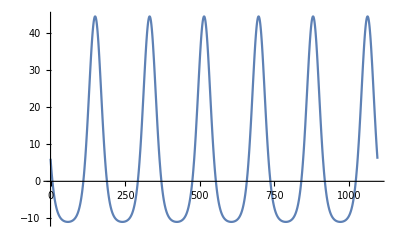

```mathematica
R0Plot=Plot[{R0/.Pars},{t,0,plottime}]
```

```mathematica
Sol1=NDSolve[{S'[t]==b(S [t]+ Ι[t]+ RA[t]+ RT[t])-β S [t]Ι[t]- S[t] (μ+k (S [t]+ Ι[t]+  RA[t]+ RT[t]))+ Subscript[ω, T] RT[t],
Ι'[t]==β S [t]Ι[t]-γ Ι[t] - Ι[t](μ+k (S [t]+ Ι[t]+ RA[t]+ RT[t])),
RA'[t]==γ Ι[t]- RA[t](μ+k (S [t]+ Ι[t]+  RA[t]+ RT[t]))- Subscript[ω, A] RA[t],
RT'[t]==Subscript[ω, A] RA[t]-RT[t](μ+k (S [t]+ Ι[t]+  RA[t]+ RT[t]))- Subscript[ω, T] RT[t],
S[0]==999,Ι[0]==1,RA[0]==0, RT[0]==0}/.Pars,{S[t],Ι[t],RA[t], RT[t]},{t,0,plottime}]
```

{{S[t]→InterpolatingFunction[…][t],Ι[t]→InterpolatingFunction[…][t],RA[t]→InterpolatingFunction[…][t],RT[t]→InterpolatingFunction[…][t]}}

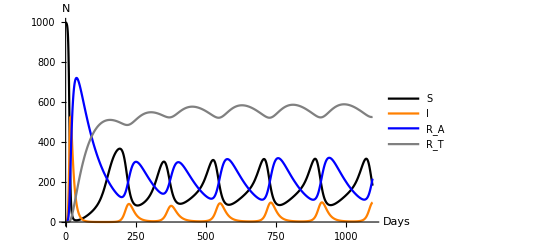

```mathematica
Plot[{S[t]/.Sol1,Ι[t]/.Sol1,RA[t]/.Sol1, RT[t]/.Sol1},{t,0,plottime},PlotLegends->{"S", "I", "R_A","R_T"}, PlotStyle->{Black, Orange, Blue, Gray}, AxesLabel->{Days, N}]
```

```mathematica
IPred= (D[RA[t]/.Sol1,t]+(Subscript[ω, A] +μ + k((S[t]/.Sol1)+(Ι[t]/.Sol1)+(RA[t]/.Sol1)+(RT[t]/.Sol1))) RA[t]/.Sol1)/γ/.Pars
```

{{10 (InterpolatingFunction[…][t] (79/6570+1/2190000(InterpolatingFunction[…][t]+InterpolatingFunction[…][t]+InterpolatingFunction[…][t]+InterpolatingFunction[…][t]))+InterpolatingFunction[…][t])}}

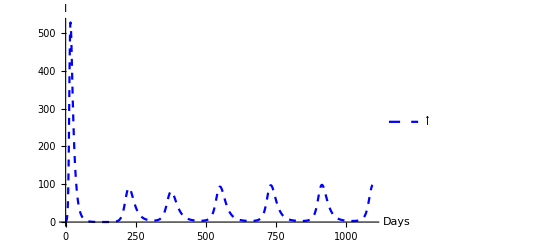

```mathematica
Pred=Plot[{IPred/.Sol1},{t,0,plottime},PlotStyle->{Blue,Dashed}, PlotRange->All, AxesLabel->{Days, Ι}, PlotLegends->{"Ι̂"} ]
```

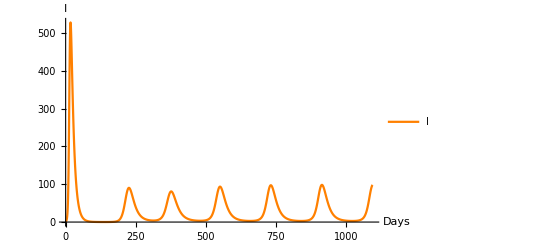

```mathematica
TRUE=Plot[{Ι[t]/.Sol1},{t,0,plottime}, PlotRange->All, PlotStyle->{Orange}, AxesLabel->{Days, Ι}, PlotLegends->{"I"}]
```

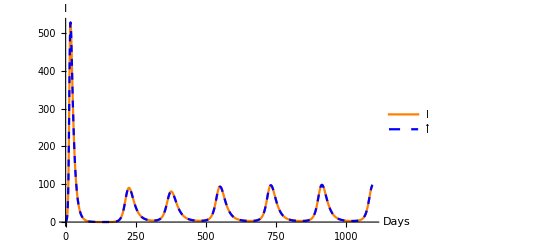

```mathematica
Show[TRUE, Pred]
```

## Solution for I for the Mechanistic Model in Proportions

N is the total population size, s is the number of susceptible individuals, ι  is the number of infected individuals, r_A is the number of seropositive  and recovered individuals, and r_T is the number of seronegative and recovered individuals.

### Change of Variables (COV) from Counts to Proportions using the quotient rule

```mathematica
ṡ=FullSimplify[FullSimplify[(Ṡ Ν-Ν̇ S)/Ν^2]/.{S->s Ν,Ι->ι Ν,RA->rA Ν, RT->rT Ν}]
```

b-b s-s β ι Ν+rT ω_T

```mathematica
ι̇=FullSimplify[FullSimplify[(Ι̇ Ν-Ν̇ Ι)/Ν^2]/.{S->s Ν,Ι->ι Ν,RA->rA  Ν, RT->rT Ν}]
```

-ι (b+γ-s β Ν)

```mathematica
OverDot[rA]=FullSimplify[FullSimplify[(OverDot[RA] Ν-Ν̇ RA)/Ν^2]/.{S->s Ν,Ι->ι Ν,RA->rA  Ν, RT->rT Ν}]
```

-b rA+γ ι-rA ω_A

```mathematica
OverDot[rT]=FullSimplify[FullSimplify[(OverDot[RT] Ν-Ν̇ RT)/Ν^2]/.{S->s Ν,Ι->ι Ν,RA->rA Ν, RT->rT Ν}]
```

rA ω_A-rT (b+ω_T)

```mathematica
FullSimplify[ṡ+ι̇+OverDot[rA]+ OverDot[rT]]/.{rA+ rT+s+ι->1}
```

0

#### Check Proportion (COV) Solution Equals Count Solution

```mathematica
Sol2=NDSolve[{s'[t]==b-b s[t]-s[t] β ι[t] Ν[t]+rT[t] Subscript[ω, T],ι'[t]==-ι[t] (b+γ-s[t] β Ν[t]),rA'[t]==γ ι[t]-rA[t] (b+Subscript[ω, A]),rT'[t]==rA[t] Subscript[ω, A]-rT[t](b+Subscript[ω, T]),Ν'[t]==b Ν[t]-Ν[t] (μ+k Ν[t]),Ν[0]==1000,s[0]==999/Ν[0],ι[0]==1/Ν[0],rA[0]==0/Ν[0],rT[0]==0/Ν[0]}/.Pars,{s[t],ι[t],rA[t],rT[t],Ν[t]},{t,0,plottime}]
```

{{s[t]→InterpolatingFunction[…][t],ι[t]→InterpolatingFunction[…][t],rA[t]→InterpolatingFunction[…][t],rT[t]→InterpolatingFunction[…][t],Ν[t]→InterpolatingFunction[…][t]}}

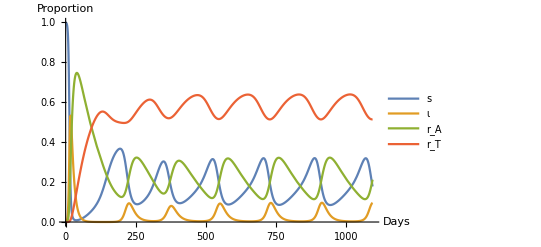

```mathematica
COVPlot=Plot[{s[t]/.Sol2,ι[t]/.Sol2,rA[t]/.Sol2, rT[t]/.Sol2},{t,0,plottime},PlotLegends->{"s", "ι", "r_A","r_T"}, AxesLabel->{Days, Proportion}]
```

```mathematica
CountSol2=NDSolve[{S'[t]==b Ν[t] -β S[t] Ι[t]- S [t](μ+k Ν[t])+ Subscript[ω, T] RT[t],Ι'[t]==β S[t] Ι[t]-γ Ι[t] - Ι[t](μ+k Ν[t] ),RA'[t]==γ Ι[t]- RA[t](μ+k Ν[t])- Subscript[ω, A] RA[t],RT'[t]==Subscript[ω, A] RA[t]- RT[t](μ+k Ν[t] )-Subscript[ω, T] RT[t],Ν'[t]==b Ν[t]-Ν[t] (μ+k Ν[t]),Ν[0]==1000,S[0]==999,Ι[0]==1,RA[0]==0, RT[0]==0}/.Pars,{S[t],Ι[t],RA[t],RT[t],Ν[t]},{t,0,plottime}]
```

{{S[t]→InterpolatingFunction[…][t],Ι[t]→InterpolatingFunction[…][t],RA[t]→InterpolatingFunction[…][t],RT[t]→InterpolatingFunction[…][t],Ν[t]→InterpolatingFunction[…][t]}}

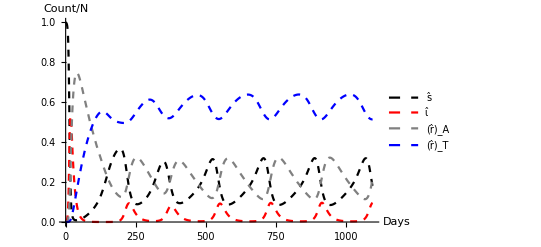

```mathematica
CountPlot=Plot[{S[t]/(S[t]+Ι[t]+RA[t]+RT[t])/.CountSol2,Ι[t]/(S[t]+Ι[t]+RA[t]+RT[t])/.CountSol2,RA[t]/(S[t]+Ι[t]+RA[t]+RT[t])/.CountSol2,RT[t]/(S[t]+Ι[t]+RA[t]+RT[t])/.CountSol2},{t,0,plottime},PlotLegends->{"ŝ", "ι̂", "(r̂)_A","(r̂)_T"}, AxesLabel->{Days, Count/N},PlotStyle->{{Black,Dashed},{Red,Dashed},{Gray,Dashed},{Blue,Dashed}}]
```

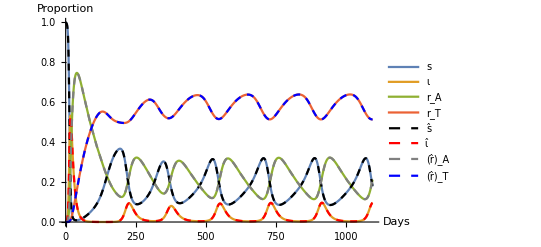

```mathematica
Show[{COVPlot,CountPlot}]
```

#### ι̂(t) = (r_A (b+ω_A)+OverDot[r_A])/γ

```mathematica
IPredProp= (D[rA[t]/.Sol2,t]+ (rA[t]/.Sol2 )(b+Subscript[ω, A]))/γ/.Pars
```

{10 ((1/90+0.00444145 ⅇ^(-4 Cos[1-(2 π t)/365]^2)) InterpolatingFunction[…][t]+InterpolatingFunction[…][t])}

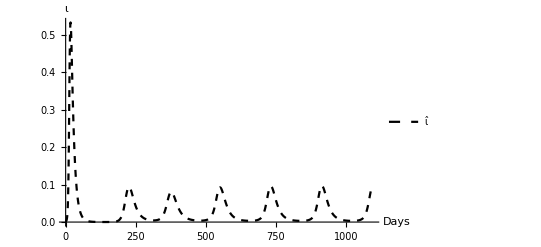

```mathematica
PredProp=Plot[{IPredProp},{t,0,plottime},PlotStyle->{Black,Dashed}, PlotRange->All, AxesLabel->{Days, ι}, PlotLegends->Placed[{"ι̂"} , {Right,Top}]]
```

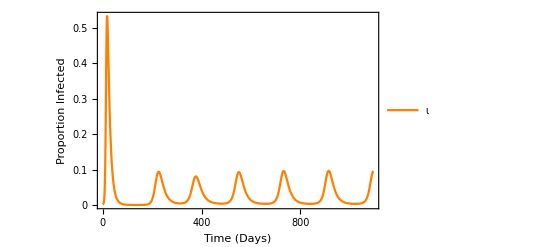

```mathematica
TRUEProp=Plot[{ι[t]/.Sol2},{t,0,plottime}, PlotRange->All, PlotStyle->{Orange}, Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Proportion Infected",None},{"Time (Days)", None}},FrameTicks->All, PlotLegends->Placed[{"ι"}, {Right,Top}]]
```

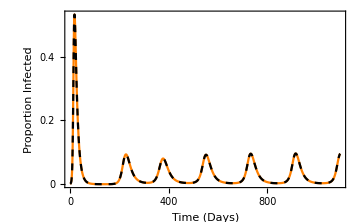

```mathematica
TrueBirth=Show[TRUEProp, PredProp]
```

#### The Solution for ι̂(t) can be approximated without the need for b(t) as long as the birth rate at any time point (t) is << ω_a.

```mathematica
IPredPropapprox= (D[rA[t]/.Sol2,t]+ (rA[t]/.Sol2 )Subscript[ω, A])/γ/.Pars
```

{10 (1/90 InterpolatingFunction[…][t]+InterpolatingFunction[…][t])}

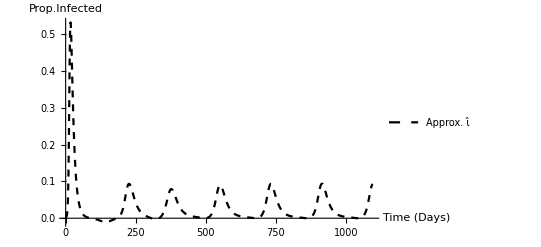

```mathematica
PredPropapprox=Plot[{IPredPropapprox},{t,0,plottime},PlotStyle->{Black,Dashed}, PlotRange->All, AxesLabel->{"Time (Days)", Prop. Infected}, PlotLegends->Placed[{"Approx. ι̂"} , {Right,Top}]]
```

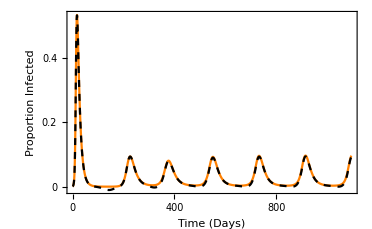

```mathematica
NoBirth=Show[TRUEProp, PredPropapprox]
```

## Sensitivity Analysis for ι̂(t) and (ι̂)_peak

The sensitivity index of ι̂(t) with respect to parameter ξ is given by (ι̂(t))_ξ=(∂ι̂(t))/(∂ξ). To find the sensitivity of the predicted peak timing with to parameter ξ , we find where (ι̂(t))_ξ is equal to zero.

```mathematica
rAdata=C2-C1 Exp[-s Cos[ π f t- ψ]^2]
```

C2-C1 ⅇ^(-s Cos[f π t-ψ]^2)

```mathematica
Parsnew={C1->1/2, C2->1/2, γ->1/10, f->2/365, ψ->0,Subscript[ω, A]->1/90,s->0.5}
```

{C1→1/2,C2→1/2,γ→1/10,f→2/365,ψ→0,ω_A→1/90,s→0.5}

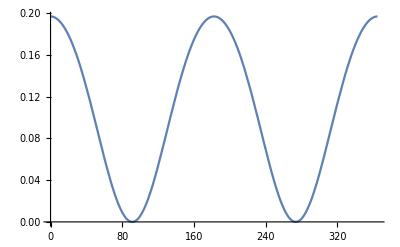

```mathematica
Plot[rAdata /. Parsnew, {t,0,365}]
```

```mathematica
ιhat=(rAdata (b+Subscript[ω, A] )+ D[rAdata,t])/γ
```

(-2 C1 ⅇ^(-s Cos[f π t-ψ]^2) f π s Cos[f π t-ψ] Sin[f π t-ψ]+(C2-C1 ⅇ^(-s Cos[f π t-ψ]^2)) (b+ω_A))/γ

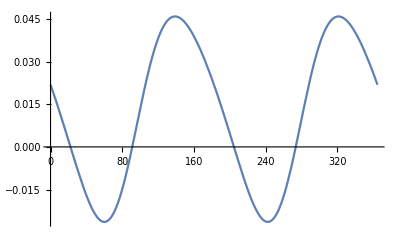

```mathematica
Plot[{ιhat/.Parsnew/.b->0},{t,0,365}]
```

```mathematica
ιhatD=D[ιhat,Subscript[ω, A]]
```

(C2-C1 ⅇ^(-s Cos[f π t-ψ]^2))/γ

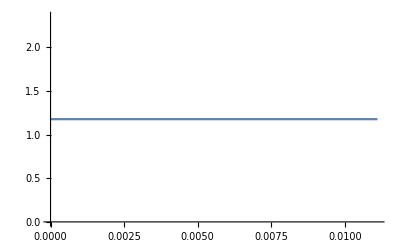

```mathematica
Plot[{ιhatD/.{C1->0.5, C2->0.5, γ->1/10, f->2/365, ψ->0, s->0.5,t->139.0031905514053}},{Subscript[ω, A],0,1/90}]
```

```mathematica
ιhat'=D[ιhat,t]/.{C1->0.5, C2->0.5, γ->1/10, f->2/365, ψ->0, b->0}
```

10 (-0.000296329 ⅇ^(-s Cos[(2 π t)/365]^2) s Cos[(2 π t)/365]^2+0.000296329 ⅇ^(-s Cos[(2 π t)/365]^2) s Sin[(2 π t)/365]^2-0.000592658 ⅇ^(-s Cos[(2 π t)/365]^2) s^2 Cos[(2 π t)/365]^2 Sin[(2 π t)/365]^2-0.0172142 ⅇ^(-s Cos[(2 π t)/365]^2) s Cos[(2 π t)/365] Sin[(2 π t)/365] ω_A)

```mathematica
FullSimplify[Solve[ιhat'==0,t]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→ConditionalExpression[116.183 ArcTan[Root[5.70051×10^23+(-2.2802×10^24+4.56041×10^24 s) #1^2+(-5.70051×10^24-9.12082×10^24 s) #1^4+(-2.2802×10^24+4.56041×10^24 s) #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,1]]+365. C[1], C[1]∈ℤ]},{t→ConditionalExpression[116.183 ArcTan[Root[5.70051×10^23+(-2.2802×10^24+4.56041×10^24 s) #1^2+(-5.70051×10^24-9.12082×10^24 s) #1^4+(-2.2802×10^24+4.56041×10^24 s) #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,2]]+365. C[1], C[1]∈ℤ]},{t→ConditionalExpression[116.183 ArcTan[Root[5.70051×10^23+(-2.2802×10^24+4.56041×10^24 s) #1^2+(-5.70051×10^24-9.12082×10^24 s) #1^4+(-2.2802×10^24+4.56041×10^24 s) #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,3]]+365. C[1], C[1]∈ℤ]},{t→ConditionalExpression[116.183 ArcTan[Root[5.70051×10^23+(-2.2802×10^24+4.56041×10^24 s) #1^2+(-5.70051×10^24-9.12082×10^24 s) #1^4+(-2.2802×10^24+4.56041×10^24 s) #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,4]]+365. C[1], C[1]∈ℤ]},{t→ConditionalExpression[116.183 ArcTan[Root[5.70051×10^23+(-2.2802×10^24+4.56041×10^24 s) #1^2+(-5.70051×10^24-9.12082×10^24 s) #1^4+(-2.2802×10^24+4.56041×10^24 s) #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,5]]+365. C[1], C[1]∈ℤ]},{t→ConditionalExpression[116.183 ArcTan[Root[5.70051×10^23+(-2.2802×10^24+4.56041×10^24 s) #1^2+(-5.70051×10^24-9.12082×10^24 s) #1^4+(-2.2802×10^24+4.56041×10^24 s) #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,6]]+365. C[1], C[1]∈ℤ]},{t→ConditionalExpression[116.183 ArcTan[Root[5.70051×10^23+(-2.2802×10^24+4.56041×10^24 s) #1^2+(-5.70051×10^24-9.12082×10^24 s) #1^4+(-2.2802×10^24+4.56041×10^24 s) #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,7]]+365. C[1], C[1]∈ℤ]},{t→ConditionalExpression[116.183 ArcTan[Root[5.70051×10^23+(-2.2802×10^24+4.56041×10^24 s) #1^2+(-5.70051×10^24-9.12082×10^24 s) #1^4+(-2.2802×10^24+4.56041×10^24 s) #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,8]]+365. C[1], C[1]∈ℤ]}}

```mathematica
fourthsolfree=116.1831084570836 ArcTan[Root[5.7005122040658496*^23+(-2.2802048816263398*^24+4.56040976325268*^24 s) #1^2+(-5.70051220406585*^24-9.12081952650536*^24 s) #1^4+(-2.2802048816263398*^24+4.56040976325268*^24 s) #1^6+5.7005122040658496*^23 #1^8+6.623032276659112*^25 #1 Subscript[ω, A]+6.623032276659112*^25 #1^3 Subscript[ω, A]-6.623032276659112*^25 #1^5 Subscript[ω, A]-6.623032276659112*^25 #1^7 Subscript[ω, A]&,4]]+365. C[1]/.{C[1]->0,s->0.5}
```

0.+116.183 ArcTan[Root[5.70051×10^23+2.68435×10^8 #1^2-1.02609×10^25 #1^4+2.68435×10^8 #1^6+5.70051×10^23 #1^8+6.62303×10^25 #1 ω_A+6.62303×10^25 #1^3 ω_A-6.62303×10^25 #1^5 ω_A-6.62303×10^25 #1^7 ω_A&,4]]

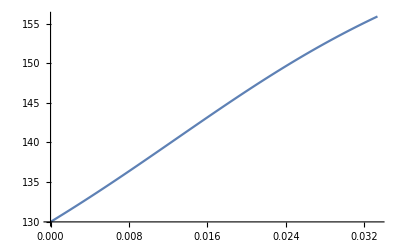

```mathematica
Plot[fourthsolfree,{Subscript[ω, A],0,1/30}]
```